```mathematica
Sum[(9+6 n)x^n/(n!), {n, 0, ∞}]
```

3 ⅇ^x (3+2 x)

```mathematica
αexp[t_, {α_, λ_}] := α E^(-I t) - 3I λ α t(1+Abs[α]^2);
```

```mathematica
α2exp[t_, {α_, λ_}]:= α^2 E^(-2I t)-3I λ α^2 t(3+2 Abs[α]^2);
```

```mathematica
σexp[t_, {α_, λ_}]:=α2exp[t, {α, λ}] - αexp[t, {α, λ}]^2;
```

```mathematica
σexp2[t_, {α_, λ_}]:=λ (6 ⅈ ⅇ^(-ⅈ t) t α^2 (1+Abs[α]^2)-3 ⅈ t α^2 (3+2 Abs[α]^2));
```

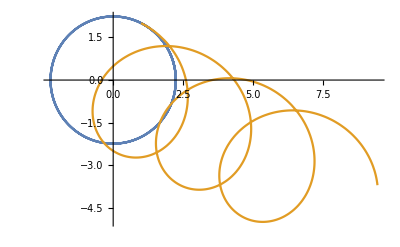

```mathematica
ParametricPlot[{ReIm@((1+2I )E^(-I t)),ReIm@αexp[t, {1+2I, 0.01}]}, {t, 0, 20}, PlotRange->All]
```

```mathematica
a[n_]:=3/4(2 n^2+2n+1);
```

```mathematica
a[n+2]-a[n]//Simplify
```

9+6 n